## Section | Quantum coherence and correlation functions

This chapter introduces the concept of coherence functions by first establishing a classical framework before transitioning to a quantum mechanical description of an atom interacting with an electromagnetic field. Proceeding to define first-order correlation and coherence, subsequently extending these principles to second-order coherence. We explore how, in the context of a single field, second-order coherence relates directly to photon statistics of quantum states of light

### Classical coherence functions

Consider the Young’s two slit experiment setup

The electric field on the detector(screen) at time t can be written as the superposition of the fields incoming from the slits at times t_1=t-s_1/c and t_2=t-s_2/c. The constants K_1,K_2 are geometric factors.

E(r,t)=K_1 E(r_1,t_1)+K_2 E(r_2,t_2)

Optical light detectors have a long response time so what is measured effectively is the average intensity

I(r)=⟨|E(r,t)|^2⟩

The time average of a function f(t) is defined as:

⟨f(t)⟩=lim_(T→∞) 1/T∫_0^T f(t)ⅆt

Defining a time expectation function:

```mathematica
TimeExpectation[f_]:=Limit[Integrate[f,{t,0,T}]/T,T->∞]
```

For example, for the function (Sin(t))^2 we get the expected result of 1/2:

```mathematica
TimeExpectation[Sin[t]^2]
```

1/2

Or a general cosine function:

```mathematica
Simplify[TimeExpectation[Cos[t m x ]^2],Element[{m,x,a},Reals]]
```

1/2

The intensity can be expressed as:

I(r)=(|K_1|)^2⟨|E(r_1,t_1)|^2⟩+(|K_2|)^2⟨|E(r_2,t_2)|^2⟩+
                2 Re[K_1^*K_2⟨E^*(r_1,t_1)E(r_2,t_2)⟩]

the first two terms are related to intensities from each slit (I_1, I_2), and the last term is the interference term

Let x_i=r_i,t_i, the first order normalized coherence function can be defined as:

γ^(1)(x_1,x_2)=⟨E^*(x_1)E(x_2)⟩/(√(⟨(|E(x_1)|)^2⟩⟨(|E(x_2)|)^2⟩))

The intensity at the screen can be rewritten in terms of the coherence function, using the polar forms of the complex numbers K_1,K_2 ,and defining θ=ψ_1-ψ_2 the phase difference related to path length difference

I(r)=I_1+I_2+2 √(I_1 I_2)Re[K_1 K_2 γ^(1)(x_1,x_2)]

I(r)=I_1+I_2+2 √(I_1 I_2)|γ^(1)(x_1,x_2)|cos(Φ_12-θ)

When |γ^(1)(x_1,x_2)|=1 there is complete coherence, |γ^(1)(x_1,x_2)|=0 means there is no coherence at all, intermediate values are related to partial coherence

Fringe visibility is defined as:

𝒱=(I_max-I_min)/(I_max+I_min)

So we can express the visibility  in terms of the first order coherence function:

```mathematica
With[{Imax = Subscript[I, 1]+Subscript[I, 2]+√(2 Subscript[I, 1] Subscript[I, 2]) Abs[γ1],Imin= Subscript[I, 1]+Subscript[I, 2]-√(2 Subscript[I, 1] Subscript[I, 2]) Abs[γ1]},(Imax-Imin)/(Imax+Imin)]//Simplify//TraditionalForm
```

(√2 √(I_1 I_2) Abs[γ1])/(I_1+I_2)

when |γ^(1)|=1, the maximum value of the visibility is (√(2 I_1 I_2))/(I_1+I_2) , and clearly the minimum is zero where there is complete incoherence

Consider monochromatic light propagating in the z direction:

```mathematica
Efield[z_,t_]:=E0 ⅇ^(ⅈ(k z - ω t))
```

Electric field at times t and t+τ:

```mathematica
{Efield[z,t],Efield[z,t+τ]}
```

{ⅇ^(ⅈ (k z-t ω)) E0,ⅇ^(ⅈ (k z-(t+τ) ω)) E0}

Calculate ⟨E*(z,t)E(z,t+τ)⟩, at position z and times t and t+τ:

```mathematica
TimeExpectation[ComplexExpand@Conjugate@Efield[z,t]Efield[z,t+τ]]
```

ⅇ^(-ⅈ τ ω) E0^2

The auto-correlation function without considering position is ⟨E^*(t)E(t+τ)⟩.
Hence γ^(1)(τ)=γ^((1)*)(-τ)=ⅇ^(-ⅈ ω t), which means|γ^(1)(τ)|=1 denoting temporal coherence

A more complete model of “monochromatic” radiation includes random phase contributions of light produced by excited atoms when decay. If we call τ_0 the coherence time of the source, that is inversely proportional to the width of atomic the spectral lines. We can introduce a function ψ(t) that represents a random step function that has a value from 0 to 2π with some period τ_0

Define ψ(t):

```mathematica
psi[t_?NumericQ,t0_?NumericQ,s_:42]:=BlockRandom[SeedRandom[Floor[t/t0]+s];RandomReal[{0,2 Pi}]]
```

Visualize the random phase ψ(t) for τ_0=1

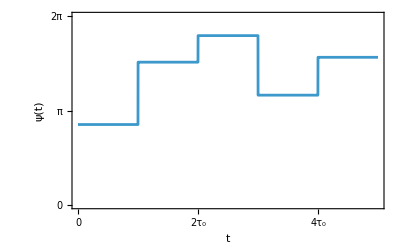

```mathematica
Plot[psi[t,1],{t,0,5},Frame->True,FrameLabel->{"t","ψ(t)"},LabelStyle->14,PlotRange->{0,2 π},FrameTicks->{{{{0,0},{π,"π"},{2 π,"2π"}},None},{Table[{i,If[i==0,0,Row[{i,"\!\(\*SubscriptBox[\(τ\), \(0\)]\)"}]]},{i,0,5}],None}},ImageSize->400]
```

Phase difference ψ(t)-ψ(t+τ) for  τ_0=1, τ=0.1

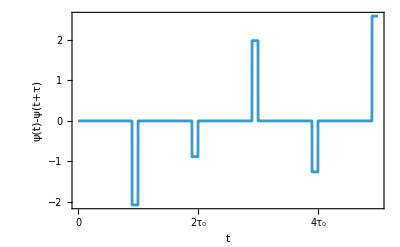

```mathematica
Plot[psi[t,1]-psi[t+0.1,1],{t,0,5},Frame->True,FrameLabel->{"t","ψ(t)-ψ(t+τ)"},FrameTicks->{{Automatic,None},{Table[{i,If[i==0,0,Row[{i,"\!\(\*SubscriptBox[\(τ\), \(0\)]\)"}]]},{i,0,5}],None}},ImageSize->400,LabelStyle->14]
```

So we can analyze the following electric field:

E(z,t)=E_0 e^(ⅈ(k z-ω t))e^(ⅈ ψ(t))

Then γ^(1) takes the form:

γ^(1)(τ)=e^(-ⅈω τ)1/T lim_(T→∞) ∫_0^T e^ⅈ[ψ(t+τ)-ψ(t)]ⅆt

We can plot the real part of the integrand(without diving by T) varying the relation between τ_0 and τ to gain some intuition of the result. When τ approaches 0 the integrand is 1, and when τ->τ_0 looks uniformly random from -1 to 1 so the integral in the limit of T→ ∞ should be 0

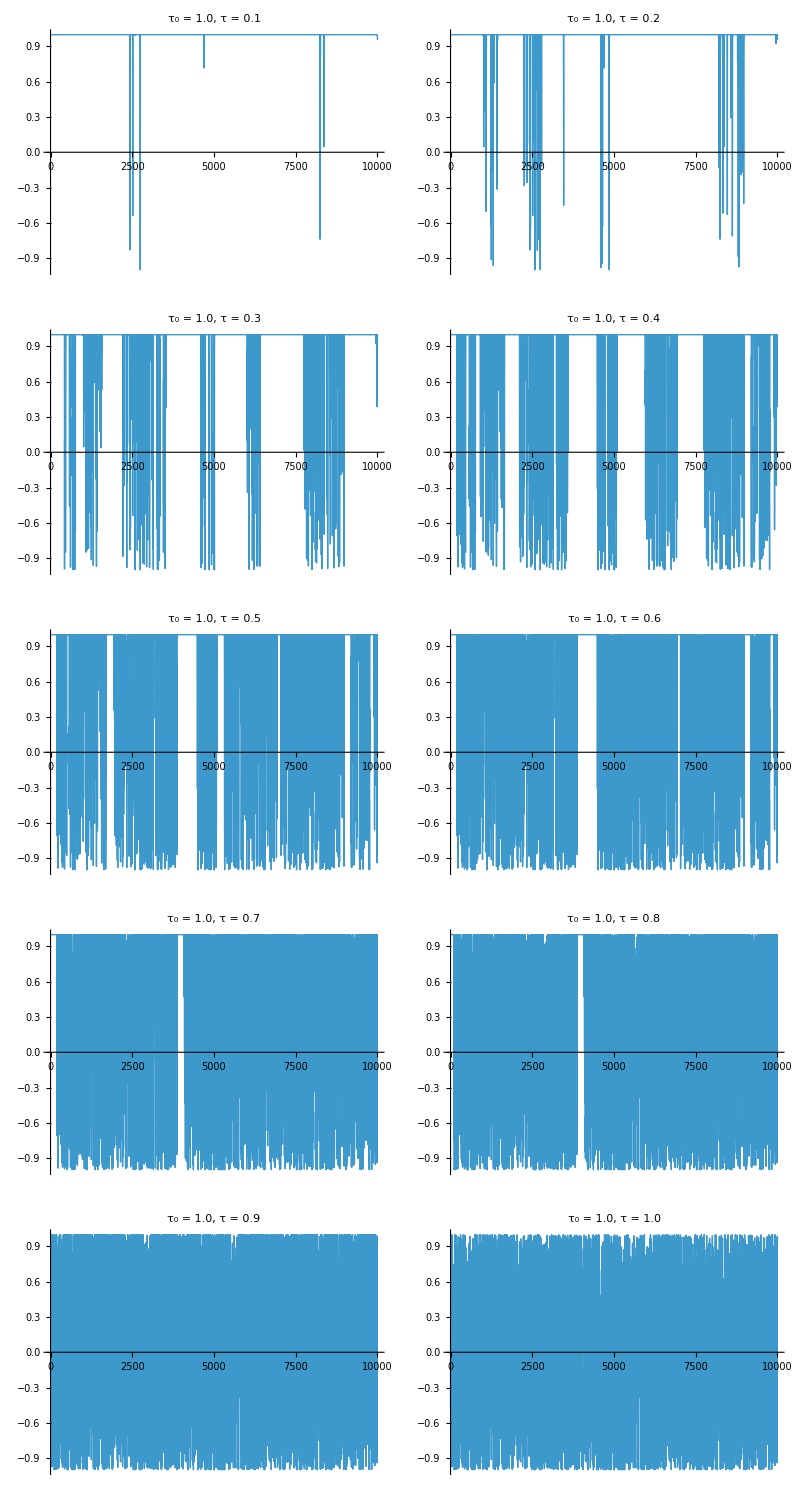

```mathematica
Grid@Partition[Table[Plot[Re[ⅇ^(ⅈ(psi[t,1]-psi[t+i 0.1,1]))],{t,0,10000},PlotRange->All,PlotStyle->Thin,PlotLabel->StringTemplate["τ_0 = ``, τ = ``"][1.,0.1 i]],{i,10}],{2}]
```

It can be shown that the integral evaluates to

I=Piecewise[{{(1-τ/τ_0) |     τ<τ_0
0 |     τ≥τ_0, }}]

For example, lets perform the numerical integration for τ_0=1,τ=0.5, we should get a value close to 0.5:

```mathematica
With[{T=10^6},1/T NIntegrate[Re[Exp[ⅈ(psi[t,1]-psi[t+0.5,1])]],{t,0,T},Method->"MultiPeriodic"]]//Quiet
```

0.503698

So | γ^(1)(τ)|=1-τ/τ_0 for τ <τ_0, and zero otherwise. So if the delay is longer than the coherence time of the source there is just no coherence at all

Other model is the collision broadened light such that has a Lorentzian power spectrum centered at ω_0. This case has the following autocorrelation function

⟨E^*(t)E(t+τ)⟩=E_0^2 e^(-ⅈω τ-|τ|/τ_0)

One way to represent this calculation is:

```mathematica
autocorrelation=E0^2 Exp[-ⅈ ω0 τ] Expectation[Exp[ⅈ δϕ],δϕ\[Distributed]NormalDistribution[0,√((2 Abs[τ])/τ0)]]
```

ⅇ^(-ⅈ τ ω0-Abs[τ]/τ0) E0^2

Get the Lorentzian functional form from the Fourier transform:

```mathematica
FourierTransform[autocorrelation,τ,ω]
```

(E0^2 √(2/π) τ0)/(1+τ0^2 (ω-ω0)^2)

From this γ^(1)(τ)=ⅇ^(-ⅈ ω_0 τ - (|τ|)/τ_0), which clearly has magnitude between 0 and 1 as expected, |γ^(1)(τ)|→0 when τ→ ∞ which means increasing the time delay reduces the coherence. We can see |τ|<<τ_0 then |γ^(1)(τ)|→1, also if the average collision time τ_0 is reduced the coherence goes to 0 faster when increasing τ.

### Quantum approach to coherence functions

When describing the theory of coherence in quantum optics, the measuring device can absorb photons. If we think of the detector as some atom, then the atom can be excited by the field from a band of wavelengths. The coupling of the atom and the quantized field can be described with the electric dipole interaction with Hamiltonian H^(I).

In this model the electric field can be written using Heisenberg picture and the long-wavelength approximation (λ >> atom size) as

Ê(r,t)≈ⅈ∑_(k,s) √((ℏ ω_k)/(2 ε_0 V))e_ks[(â)_ks(t)-(â)_ks^†(t)]

Which has a component describing photon absorption related to the annihilation operator, this component is also called the positive frequency part

(Ê)^(+)(r,t)=ⅈ∑_(k,s) ((ℏ ω_k)/(2 ε_0 V))^(1/2)e_ks(â)_ks(t)

Assuming the atom is in some initial state |g⟩ and transitions to a ionized atomic state|e⟩, and the field transitions to some state |i⟩ to |f⟩. Letting |I⟩ =|g⟩ |i⟩ and |F⟩ = |e⟩ |g⟩ the transition probability for the full system is |⟨F|H^(I)|I⟩|^2, and for the field is |⟨f|E^(+)(r,t)|i⟩|^2. We only care about the final state of the detector not the field, so we have to sum over all the states |f⟩ which without loss of generality assume to be complete

Performing the sum we get:

⟨i|(Ê)^(-)(r,t)·(Ê)^(+)(r,t)|i⟩

Or for mixed states ρ_F:

Tr{(ρ̂)_F(Ê)^(-)(r,t)·(Ê)^(+)(r,t)}

Treating the fields as scalars(same polarization) we can define the quantum version:

G^(1)(x,x)=Tr{ρ (Ê)^(-)(x)(Ê)^(+)(x)}

Referring to the previous diagram of Young’s interference we can similarly consider the quantum analog E^(+)(r,t)=K_1 E^(+)(r_1,t_1)+K_2 E^(+)(r_2,t_2) using positive frequency operators. So the intensity at the detector is

I(r,t)=Tr{ρ̂(Ê)^(-)(r,t)(Ê)^(+)(r,t)}=
|K_1|^2 G^(1)(x_1,x_1)+(|K_2|)^2 G^(1)(x_2,x_2)+2 Re[K_1^*K_2 G^(1)(x_1,x_2)]

G^(1)(x_i,x_i)   i=1,2 is the intensity at the detector coming from x_i, and the correlation of light arriving from x_1 and x_2 is G^(1)(x_1,x_2) (interference)

Analogously to the classical γ^(1), the normalized first-order coherence function is:

g^(1)(x_1,x_2)=(G^(1)(x_1,x_2))/([G^(1)(x_1,x_1)G^(1)(x_2,x_2)]^(1/2))

where 0<=|g^(1)|<=1 determines if it is coherent, partial coherence or incoherent

Pick a Fock state number:

```mathematica
n= RandomInteger[{1,$FockSize-1}];
```

G^(1)(x,x)=n for a Fock state:

```mathematica
G1Correlation[FockState[n],{{r,t},{r,t}}]==n
```

True

G^(1)(x_1,x_2) for a Fock state:

```mathematica
G1Correlation[FockState[n],{{r1,t1},{r2,t2}}]//FullSimplify
```

7 ⅇ^(ⅈ (ω (t1-t2)+k.(-r1+r2)))

clearly when normalizing we divide by n , hence |g^(1)(x_1,x_2)|=1

Pick a random complex amplitude:

```mathematica
α = RandomComplex[];
```

G^(1)(x,x)=|α|^2 for a coherent state:

```mathematica
Chop[G1Correlation[CoherentState[][α],{{r,t},{r,t}}]-Abs[α]^2]
```

0

Calculate g^(1)(x_1,x_2) for the state |α⟩:

```mathematica
g1Coh=With[{s=CoherentState[][α],pts={{r1,t1},{r2,t2}}},G1Correlation[s,pts]/Sqrt[Times@@(G1Correlation[s,{#,#}]&/@pts)]];
```

We see we also get |g^(1)(x_1,x_2)|=1:

```mathematica
ComplexExpand@Abs[g1Coh]
```

1.+0. ⅈ

Calculate g^(1)(x_1,x_2) for thermal light with n^—=1 :

```mathematica
g1Thermal=With[{s=ThermalState[1],pts={{r1,t1},{r2,t2}}},G1Correlation[s,pts]/Sqrt[Times@@(G1Correlation[s,{#,#}]&/@pts)]]
```

ⅇ^(-ⅈ (-ω t1+k.r1)+ⅈ (-ω t2+k.r2))

So we see Fock states, coherent states and thermal light are first-order coherent
which implies the factorization G^(1)(x_1,x_2)=⟨E^(-)(x_1)E^(+)(x_2)⟩ =⟨E^(-)(x_1)⟩⟨E^(+)(x_2)⟩

### Higher-order coherence functions

We saw for a single-mode field Fock states and coherent states are first-order coherent, but that says nothing about their photon statistics, for these states that must be different

From a quantum perspective we will see coherent states (such coming from a stabilized laser) are second-order coherent and thermal light presents photon bunching (a pair of photons coming together)

Three types of behavior of photon statistics

Following a really similar approach when defining G^(1), we define G^(2) the second-order quantum correlation as

G^(2)(x_1,x_2;x_2,x_1)=Tr{ρ̂(Ê)^(-)(x_1)(Ê)^(-)(x_2)(Ê)^(+)(x_2)(Ê)^(+)(x_1)}

which is the ensemble average of I(x_1)I(x_2) following normal order of field operators

Similarly the second-order quantum coherence function is:

g^(2)(x_1,x_2;x_2,x_1)=(G^(2)(x_1,x_2;x_2,x_1))/(G^(1)(x_1,x_1)G^(1)(x_2,x_2))

A state of light is second-order coherent if |g^(2)(x_1,x_2)|=1, such that the factorization G^(2)(x_1,x_2)=G^(1)(x_1,x_1)G^(1)(x_2,x_2) holds

If the position has a fixed value, g^(2) depends only on the time difference τ

g^(2)(τ)=⟨(Ê)^(-)(t)(Ê)^(-)(t+τ)(Ê)^(+)(t+τ)(Ê)^(+)(t)⟩/(⟨(Ê)^(-)(t)(Ê)^(+)(t)⟩⟨(Ê)^(-)(t+τ)(Ê)^(+)(t+τ)⟩)

For single-mode states the second-order coherence assumes a simple form

g^(2)(τ)=⟨(â)^†(â)^†â â⟩/(⟨(â)^†â⟩^2)=⟨n̂(n̂-1)⟩/⟨n̂⟩^2

and does not depend on τ, so g^2(τ)=g^2(0) which can be easier to calculate, and it relates to photon statistics and not to temporal correlations

For a Fock state n>=1, the g^(2)(0) has the value of  1-1/n:

```mathematica
FindSequenceFunction[Array[G2Coherence@*FockState,$FockSize-1,1]][n]//Apart
```

1-1/n

For the vacuum state g^(2) is not defined from the mathematical definition, we can also see that plugging n=0 in the above formula. However, the value that makes sense from a experimental point of view is just 0, there cannot be coherence with a no photons state

```mathematica
G2Coherence[FockState[0]]//Quiet
```

Indeterminate

Evidently, the superposition 1/(√2)(|0⟩ + |1⟩) has zero g^(2):

```mathematica
G2Coherence[QuantumState["+",$FockSize]]
```

0

Also for the mixed state of the number states 0 and 1:

```mathematica
1/2Total@Array[FockState[#]["MatrixState"]&,2,0]
```

1/2 00+1/2 11

```mathematica
G2Coherence[%]
```

0

Now calculate g^(2) for a coherent state  |α⟩:

```mathematica
G2Coherence[CoherentState[][1.2]]
```

1.

g^(2)=1, verifying that a coherent state is second-order coherent and the photon arrivals can be described as random with a Poisson distribution

Depending on the value of α and the truncation size used, we see numerical error can be relevant:

```mathematica
g2s = Table[G2Coherence[CoherentState[m][α]],{m,{12,16,24}},{α,0.1,4,0.1}];
```

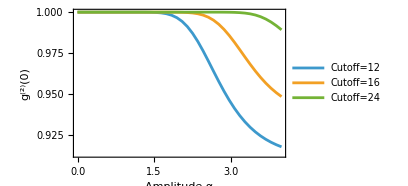

```mathematica
ListLinePlot[g2s,]
```

For a thermal state g^(2)=2, so we say thermal light is not second-order coherent and has higher probability of detecting coincident photons

Second order coherence for a symbolic thermal state depending on the mean number of photons:

```mathematica
thermalG2 = G2Coherence[ThermalState[x,30]];
```

We can also see the effect of truncation numerical error:

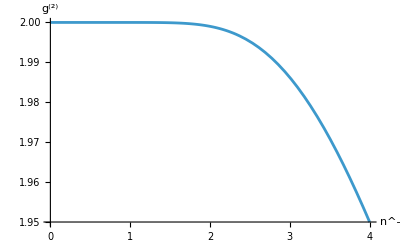

```mathematica
Plot[thermalG2,{x,0,4},AxesLabel->{"n^—","g^(2)"}]
```

Other interesting example is to analyze the state (1-p)|0⟩⟨0|+p|2⟩⟨2|:

```mathematica
state = (1-p)FockState[0]["MatrixState"]+p FockState[2]["MatrixState"]
```

(1-p)00+p22

Calculate the second-order coherence:

```mathematica
G2Coherence[state]
```

1/(2 p)

if p<<1 ,  g^(2) can take big values this is extreme bunching based on the fact the state is almost always in the vacuum and suddenly two photons appear

Summarizing the results

```mathematica
Grid[{{Style["Value",Bold],Style["Photon statistics",Bold]},{Row[{("g")^("(2)")," = 1"}],"Poissonian statistics (coherent light)"},{Row[{("g")^("(2)")," < 1"}],"Sub-Poissonian (non-classical light)"},{Row[{("g")^("(2)")," > 1"}],"Super-Poissonian (bunching, thermal light)"},{Row[{("g")^("(2)")," = 0"}],"Single-photon state"}},Frame->All,Spacings->{2,1},Background->{None,{LightGray,{White}}},Alignment->{Center,Left},ItemStyle->{FontFamily->"Times",FontSize->14}]
```

Value | Photon statistics
g^(2) = 1 | Poissonian statistics (coherent light)
g^(2) < 1 | Sub-Poissonian (non-classical light)
g^(2) > 1 | Super-Poissonian (bunching, thermal light)
g^(2) = 0 | Single-photon state

It is worth noting that for multi-mode fields that have a width of frequencies g^(2)(τ)!= g^(2)(0). The plot below illustrates the theoretical curve for a typical single-photon wave packet. In experimental quantum optics, achieving a low g^(2)(0) value is one of the figures of merit for validating high-purity single-photon sources.

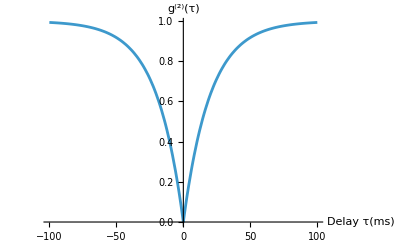

```mathematica
Plot[1-ⅇ^(-Abs[x]0.05),{x,-100,100},AxesLabel->{"Delay τ(ms)","g^(2)(τ)"},LabelStyle->14,ImageSize->400]
```

In general, the n-th order quantum correlation function is:

G^(n)(x_1,…x_n;x_n,…x_1)=Tr{ρ̂(Ê)^(-)(x_1)…(Ê)^(-)(x_n)(Ê)^(+)(x_n)…(Ê)^(+)(x_1)}

And the n-th order coherence function can be defined as:

g^(n)(x_1,…x_n;x_n,…x_1)=(G^(n)(x_1,…x_n;x_n,…x_1))/(G^(1)(x_1,x_1)…G^(1)(x_n,x_n))

##### Initialization

Load quantum framework functions:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load quantum framework functions for  second quantization:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Vocabulary

G2Coherence |   | Computes g^(2)(0)for a single-mode quantum state
G1Correlation |   | Computes the first-order correlation G^(1)(x_1,x_2) for a single-mode quantum state

Exercises

Analyze the coherent properties (first and second order) of the state 1/(√2)(|α⟩ + |-α⟩) that is a superposition of coherent states. Try to approach the limit of large α

Solution

Define the state symbolically, use a truncation size big enough:

state =1/(√2)(CoherentState[60][α]+CoherentState[60][-α]);

First order coherence:

firstOrder =G1Correlation[state,{{r,t},{r,t}}];

Plot[firstOrder/α^2,{α,1,5}]

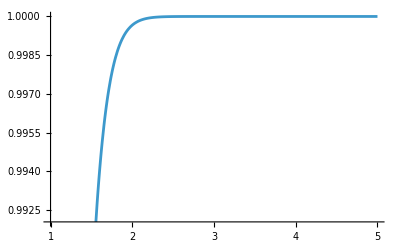

Second order coherence:

secondOrder = G2Coherence[state];

Plot[secondOrder,{α,1,5}]

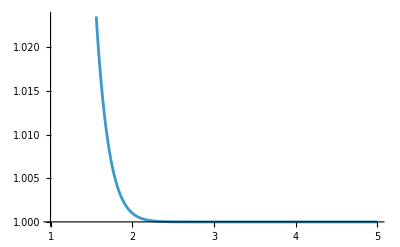

Compute the second order coherence for a uniform superposition state in the truncated Fock space, if the dimension is ≥ 3 find a general formula. We expect that the value of such state is > 1 if the truncation size is big enough

Solution

Find the formula:

FindSequenceFunction[Table[G2Coherence[QuantumState["UniformSuperposition",n]],{n,3,15}],n-2]

(4 (-2+n))/(3 (-1+n))

Plot the values:

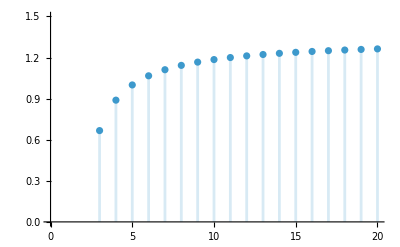

```mathematica
DiscretePlot[%,{n,3,20},PlotRange->{0,1.5}]
```

References

Use Chicago Style in your reference section. We have provided this References section for those who prefer in chapter reference sections.  However, generally we preferences to be at the end of the book as a Bibliography.  For citations within chapters, please use standard (Author, Date) in-text citation.